```mathematica
f[x_]:=a*E^(-(x-b)^2/(2*c^2))
```

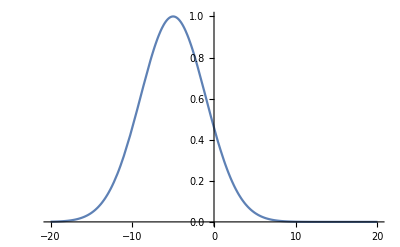

```mathematica
a=1;
b=-5;
c=4;
Plot[f[x],{x,-20,20},PlotRange->Full]
```

```mathematica
TraditionalForm[f[x]]
```

ⅇ^(-x^2/32)

```mathematica
probs=N@f[Range[-10,10]]
```

{0.0439369,0.0795595,0.135335,0.216265,0.324652,0.457833,0.606531,0.75484,0.882497,0.969233,1.,0.969233,0.882497,0.75484,0.606531,0.457833,0.324652,0.216265,0.135335,0.0795595,0.0439369}

```mathematica
probsNorm={Normalize[probs]}
```

{{0.0165026,0.0298824,0.0508317,0.0812289,0.121939,0.171962,0.227812,0.283517,0.331465,0.364043,0.375599,0.364043,0.331465,0.283517,0.227812,0.171962,0.121939,0.0812289,0.0508317,0.0298824,0.0165026}}

```mathematica
probNormGraph=Transpose@Join[{Range[-10,10]},probsNorm]
```

{{-10,0.0165026},{-9,0.0298824},{-8,0.0508317},{-7,0.0812289},{-6,0.121939},{-5,0.171962},{-4,0.227812},{-3,0.283517},{-2,0.331465},{-1,0.364043},{0,0.375599},{1,0.364043},{2,0.331465},{3,0.283517},{4,0.227812},{5,0.171962},{6,0.121939},{7,0.0812289},{8,0.0508317},{9,0.0298824},{10,0.0165026}}

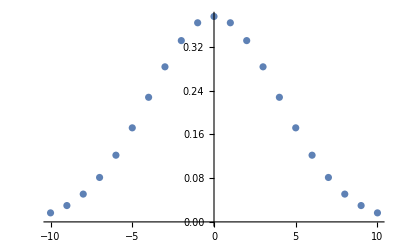

```mathematica
ListPlot[probNormGraph]
```